```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+k <-->C

c+e ->a+e
*)
```

```mathematica
gR=1; (*NLR growth*)
gK1=10;
gK2=10;
gK3=10;
gK4=10;
gK5=10;
gK6=10;
gK={gK1,gK2,gK3,gK4,gK5,gK6};
deltaR=1; (*NLR decay*)
deltaK=1; (*kinase decay*)
(*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=0.1;  (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

```mathematica
(*note: we use Subscript[γ, 1]=0.1 to get a larger dynamic range for E*)
```

```mathematica
e0=3; (*total effector concentration*)
```

## Equations

```mathematica
(*simple approximation: Subscript[γ, 2]>>Subscript[γ, 1], so e_i-->Ei*)
```

```mathematica
getZ[kVec_,eVec_]:=Module[{thisZ},
(* return Z*)
thisTable=Table[kVec[[i]]*eVec[[i]]/(alphaB+gamma1*eVec[[i]]),{i,Length[eVec]}];
thisZ=alphaF*gamma1*Total[thisTable];
thisZ
]
```

```mathematica
drds[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
thisZ=getZ[kVec,eVec];
gR-deltaR*rVar-rVar*thisZ+f[aVar]
]
```

```mathematica
dads[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)

thisZ=getZ[kVec,eVec];
rVar*thisZ-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
(*we'll define separate k variables, but use one deriv fn*)
dkids[rVar_,aVar_,kVec_,eVec_,kIndex_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
gK[[kIndex]]-deltaK*kVec[[kIndex]]-alphaF*rVar*kVec[[kIndex]]*gamma1*eVec[[kIndex]]/(alphaB+gamma1*eVec[[kIndex]])+fk[aVar]
]
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

```mathematica
fk[z_]:=0;(* kinase feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100,1000};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,1]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,2]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,3]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,4]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,5]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,6]==0},{rVar,guessList[[i]],0,10^8},{k1Var,guessList[[j]],0,10^8},{k2Var,guessList[[j]],0,10^8},{k3Var,guessList[[j]],0,10^8},{k4Var,guessList[[j]],0,10^8},{k5Var,guessList[[j]],0,10^8},{k6Var,guessList[[j]],0,10^8},{aVar,guessList[[k]],0,10^8}];
residual=(drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2+(dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,aVar,k1Var,k2Var,k3Var,k4Var,k5Var,k6Var}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
(*try fixing total amount of E in each step, but distributing it evenly*)
```

```mathematica
(*fixedPointList=Table[{{i/6,i/6,i/6,i/6,i/6,i/6},getFixedPoint[{i/6,i/6,i/6,i/6,i/6,i/6}]},{i,0,20,0.1}];*)
```

```mathematica
(*try fixing total amount of E in each step, but distributing it unevenly*)
```

```mathematica
maxE=(5/6)//N;
otherE=(1-maxE)/5;
```

```mathematica
fixedPointList=Table[{{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i},getFixedPoint[{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i}]},{i,0,10,.05}];
```

{0.,0.,0.,0.,0.,0.}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.,0.100099,0.100099,0.100099,0.100099,0.100099,0.100099,99.999} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,0.100001,0.100001,0.100001,0.100001,0.100001,0.100001,1000.} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.,1.00009,1.00009,1.00009,1.00009,1.00009,1.00009,99.999} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.0416667,0.00166667,0.00166667,0.00166667,0.00166667,0.00166667}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{0.0833333,0.00333333,0.00333333,0.00333333,0.00333333,0.00333333}

{0.125,0.005,0.005,0.005,0.005,0.005}

{0.166667,0.00666667,0.00666667,0.00666667,0.00666667,0.00666667}

{0.208333,0.00833333,0.00833333,0.00833333,0.00833333,0.00833333}

{0.25,0.01,0.01,0.01,0.01,0.01}

{0.291667,0.0116667,0.0116667,0.0116667,0.0116667,0.0116667}

{0.333333,0.0133333,0.0133333,0.0133333,0.0133333,0.0133333}

{0.375,0.015,0.015,0.015,0.015,0.015}

{0.416667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667}

{0.458333,0.0183333,0.0183333,0.0183333,0.0183333,0.0183333}

{0.5,0.02,0.02,0.02,0.02,0.02}

{0.541667,0.0216667,0.0216667,0.0216667,0.0216667,0.0216667}

{0.583333,0.0233333,0.0233333,0.0233333,0.0233333,0.0233333}

{0.625,0.025,0.025,0.025,0.025,0.025}

{0.666667,0.0266667,0.0266667,0.0266667,0.0266667,0.0266667}

{0.708333,0.0283333,0.0283333,0.0283333,0.0283333,0.0283333}

{0.75,0.03,0.03,0.03,0.03,0.03}

{0.791667,0.0316667,0.0316667,0.0316667,0.0316667,0.0316667}

{0.833333,0.0333333,0.0333333,0.0333333,0.0333333,0.0333333}

{0.875,0.035,0.035,0.035,0.035,0.035}

{0.916667,0.0366667,0.0366667,0.0366667,0.0366667,0.0366667}

{0.958333,0.0383333,0.0383333,0.0383333,0.0383333,0.0383333}

{1.,0.04,0.04,0.04,0.04,0.04}

{1.04167,0.0416667,0.0416667,0.0416667,0.0416667,0.0416667}

{1.08333,0.0433333,0.0433333,0.0433333,0.0433333,0.0433333}

{1.125,0.045,0.045,0.045,0.045,0.045}

{1.16667,0.0466667,0.0466667,0.0466667,0.0466667,0.0466667}

{1.20833,0.0483333,0.0483333,0.0483333,0.0483333,0.0483333}

{1.25,0.05,0.05,0.05,0.05,0.05}

{1.29167,0.0516667,0.0516667,0.0516667,0.0516667,0.0516667}

{1.33333,0.0533333,0.0533333,0.0533333,0.0533333,0.0533333}

{1.375,0.055,0.055,0.055,0.055,0.055}

{1.41667,0.0566667,0.0566667,0.0566667,0.0566667,0.0566667}

{1.45833,0.0583333,0.0583333,0.0583333,0.0583333,0.0583333}

{1.5,0.06,0.06,0.06,0.06,0.06}

{1.54167,0.0616667,0.0616667,0.0616667,0.0616667,0.0616667}

{1.58333,0.0633333,0.0633333,0.0633333,0.0633333,0.0633333}

{1.625,0.065,0.065,0.065,0.065,0.065}

{1.66667,0.0666667,0.0666667,0.0666667,0.0666667,0.0666667}

{1.70833,0.0683333,0.0683333,0.0683333,0.0683333,0.0683333}

{1.75,0.07,0.07,0.07,0.07,0.07}

{1.79167,0.0716667,0.0716667,0.0716667,0.0716667,0.0716667}

{1.83333,0.0733333,0.0733333,0.0733333,0.0733333,0.0733333}

{1.875,0.075,0.075,0.075,0.075,0.075}

{1.91667,0.0766667,0.0766667,0.0766667,0.0766667,0.0766667}

{1.95833,0.0783333,0.0783333,0.0783333,0.0783333,0.0783333}

{2.,0.08,0.08,0.08,0.08,0.08}

{2.04167,0.0816667,0.0816667,0.0816667,0.0816667,0.0816667}

{2.08333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333}

{2.125,0.085,0.085,0.085,0.085,0.085}

{2.16667,0.0866667,0.0866667,0.0866667,0.0866667,0.0866667}

{2.20833,0.0883333,0.0883333,0.0883333,0.0883333,0.0883333}

{2.25,0.09,0.09,0.09,0.09,0.09}

{2.29167,0.0916667,0.0916667,0.0916667,0.0916667,0.0916667}

{2.33333,0.0933333,0.0933333,0.0933333,0.0933333,0.0933333}

{2.375,0.095,0.095,0.095,0.095,0.095}

{2.41667,0.0966667,0.0966667,0.0966667,0.0966667,0.0966667}

{2.45833,0.0983333,0.0983333,0.0983333,0.0983333,0.0983333}

{2.5,0.1,0.1,0.1,0.1,0.1}

{2.54167,0.101667,0.101667,0.101667,0.101667,0.101667}

{2.58333,0.103333,0.103333,0.103333,0.103333,0.103333}

{2.625,0.105,0.105,0.105,0.105,0.105}

{2.66667,0.106667,0.106667,0.106667,0.106667,0.106667}

{2.70833,0.108333,0.108333,0.108333,0.108333,0.108333}

{2.75,0.11,0.11,0.11,0.11,0.11}

{2.79167,0.111667,0.111667,0.111667,0.111667,0.111667}

{2.83333,0.113333,0.113333,0.113333,0.113333,0.113333}

{2.875,0.115,0.115,0.115,0.115,0.115}

{2.91667,0.116667,0.116667,0.116667,0.116667,0.116667}

{2.95833,0.118333,0.118333,0.118333,0.118333,0.118333}

{3.,0.12,0.12,0.12,0.12,0.12}

{3.04167,0.121667,0.121667,0.121667,0.121667,0.121667}

{3.08333,0.123333,0.123333,0.123333,0.123333,0.123333}

{3.125,0.125,0.125,0.125,0.125,0.125}

{3.16667,0.126667,0.126667,0.126667,0.126667,0.126667}

{3.20833,0.128333,0.128333,0.128333,0.128333,0.128333}

{3.25,0.13,0.13,0.13,0.13,0.13}

{3.29167,0.131667,0.131667,0.131667,0.131667,0.131667}

{3.33333,0.133333,0.133333,0.133333,0.133333,0.133333}

{3.375,0.135,0.135,0.135,0.135,0.135}

{3.41667,0.136667,0.136667,0.136667,0.136667,0.136667}

{3.45833,0.138333,0.138333,0.138333,0.138333,0.138333}

{3.5,0.14,0.14,0.14,0.14,0.14}

{3.54167,0.141667,0.141667,0.141667,0.141667,0.141667}

{3.58333,0.143333,0.143333,0.143333,0.143333,0.143333}

{3.625,0.145,0.145,0.145,0.145,0.145}

{3.66667,0.146667,0.146667,0.146667,0.146667,0.146667}

{3.70833,0.148333,0.148333,0.148333,0.148333,0.148333}

{3.75,0.15,0.15,0.15,0.15,0.15}

{3.79167,0.151667,0.151667,0.151667,0.151667,0.151667}

{3.83333,0.153333,0.153333,0.153333,0.153333,0.153333}

{3.875,0.155,0.155,0.155,0.155,0.155}

{3.91667,0.156667,0.156667,0.156667,0.156667,0.156667}

{3.95833,0.158333,0.158333,0.158333,0.158333,0.158333}

{4.,0.16,0.16,0.16,0.16,0.16}

{4.04167,0.161667,0.161667,0.161667,0.161667,0.161667}

{4.08333,0.163333,0.163333,0.163333,0.163333,0.163333}

{4.125,0.165,0.165,0.165,0.165,0.165}

{4.16667,0.166667,0.166667,0.166667,0.166667,0.166667}

{4.20833,0.168333,0.168333,0.168333,0.168333,0.168333}

{4.25,0.17,0.17,0.17,0.17,0.17}

{4.29167,0.171667,0.171667,0.171667,0.171667,0.171667}

{4.33333,0.173333,0.173333,0.173333,0.173333,0.173333}

{4.375,0.175,0.175,0.175,0.175,0.175}

{4.41667,0.176667,0.176667,0.176667,0.176667,0.176667}

{4.45833,0.178333,0.178333,0.178333,0.178333,0.178333}

{4.5,0.18,0.18,0.18,0.18,0.18}

{4.54167,0.181667,0.181667,0.181667,0.181667,0.181667}

{4.58333,0.183333,0.183333,0.183333,0.183333,0.183333}

{4.625,0.185,0.185,0.185,0.185,0.185}

{4.66667,0.186667,0.186667,0.186667,0.186667,0.186667}

{4.70833,0.188333,0.188333,0.188333,0.188333,0.188333}

{4.75,0.19,0.19,0.19,0.19,0.19}

{4.79167,0.191667,0.191667,0.191667,0.191667,0.191667}

{4.83333,0.193333,0.193333,0.193333,0.193333,0.193333}

{4.875,0.195,0.195,0.195,0.195,0.195}

{4.91667,0.196667,0.196667,0.196667,0.196667,0.196667}

{4.95833,0.198333,0.198333,0.198333,0.198333,0.198333}

{5.,0.2,0.2,0.2,0.2,0.2}

{5.04167,0.201667,0.201667,0.201667,0.201667,0.201667}

{5.08333,0.203333,0.203333,0.203333,0.203333,0.203333}

{5.125,0.205,0.205,0.205,0.205,0.205}

{5.16667,0.206667,0.206667,0.206667,0.206667,0.206667}

{5.20833,0.208333,0.208333,0.208333,0.208333,0.208333}

{5.25,0.21,0.21,0.21,0.21,0.21}

{5.29167,0.211667,0.211667,0.211667,0.211667,0.211667}

{5.33333,0.213333,0.213333,0.213333,0.213333,0.213333}

{5.375,0.215,0.215,0.215,0.215,0.215}

{5.41667,0.216667,0.216667,0.216667,0.216667,0.216667}

{5.45833,0.218333,0.218333,0.218333,0.218333,0.218333}

{5.5,0.22,0.22,0.22,0.22,0.22}

{5.54167,0.221667,0.221667,0.221667,0.221667,0.221667}

{5.58333,0.223333,0.223333,0.223333,0.223333,0.223333}

{5.625,0.225,0.225,0.225,0.225,0.225}

{5.66667,0.226667,0.226667,0.226667,0.226667,0.226667}

{5.70833,0.228333,0.228333,0.228333,0.228333,0.228333}

{5.75,0.23,0.23,0.23,0.23,0.23}

{5.79167,0.231667,0.231667,0.231667,0.231667,0.231667}

{5.83333,0.233333,0.233333,0.233333,0.233333,0.233333}

{5.875,0.235,0.235,0.235,0.235,0.235}

{5.91667,0.236667,0.236667,0.236667,0.236667,0.236667}

{5.95833,0.238333,0.238333,0.238333,0.238333,0.238333}

{6.,0.24,0.24,0.24,0.24,0.24}

{6.04167,0.241667,0.241667,0.241667,0.241667,0.241667}

{6.08333,0.243333,0.243333,0.243333,0.243333,0.243333}

{6.125,0.245,0.245,0.245,0.245,0.245}

{6.16667,0.246667,0.246667,0.246667,0.246667,0.246667}

{6.20833,0.248333,0.248333,0.248333,0.248333,0.248333}

{6.25,0.25,0.25,0.25,0.25,0.25}

{6.29167,0.251667,0.251667,0.251667,0.251667,0.251667}

{6.33333,0.253333,0.253333,0.253333,0.253333,0.253333}

{6.375,0.255,0.255,0.255,0.255,0.255}

{6.41667,0.256667,0.256667,0.256667,0.256667,0.256667}

{6.45833,0.258333,0.258333,0.258333,0.258333,0.258333}

{6.5,0.26,0.26,0.26,0.26,0.26}

{6.54167,0.261667,0.261667,0.261667,0.261667,0.261667}

{6.58333,0.263333,0.263333,0.263333,0.263333,0.263333}

{6.625,0.265,0.265,0.265,0.265,0.265}

{6.66667,0.266667,0.266667,0.266667,0.266667,0.266667}

{6.70833,0.268333,0.268333,0.268333,0.268333,0.268333}

{6.75,0.27,0.27,0.27,0.27,0.27}

{6.79167,0.271667,0.271667,0.271667,0.271667,0.271667}

{6.83333,0.273333,0.273333,0.273333,0.273333,0.273333}

{6.875,0.275,0.275,0.275,0.275,0.275}

{6.91667,0.276667,0.276667,0.276667,0.276667,0.276667}

{6.95833,0.278333,0.278333,0.278333,0.278333,0.278333}

{7.,0.28,0.28,0.28,0.28,0.28}

{7.04167,0.281667,0.281667,0.281667,0.281667,0.281667}

{7.08333,0.283333,0.283333,0.283333,0.283333,0.283333}

{7.125,0.285,0.285,0.285,0.285,0.285}

{7.16667,0.286667,0.286667,0.286667,0.286667,0.286667}

{7.20833,0.288333,0.288333,0.288333,0.288333,0.288333}

{7.25,0.29,0.29,0.29,0.29,0.29}

{7.29167,0.291667,0.291667,0.291667,0.291667,0.291667}

{7.33333,0.293333,0.293333,0.293333,0.293333,0.293333}

{7.375,0.295,0.295,0.295,0.295,0.295}

{7.41667,0.296667,0.296667,0.296667,0.296667,0.296667}

{7.45833,0.298333,0.298333,0.298333,0.298333,0.298333}

{7.5,0.3,0.3,0.3,0.3,0.3}

{7.54167,0.301667,0.301667,0.301667,0.301667,0.301667}

{7.58333,0.303333,0.303333,0.303333,0.303333,0.303333}

{7.625,0.305,0.305,0.305,0.305,0.305}

{7.66667,0.306667,0.306667,0.306667,0.306667,0.306667}

{7.70833,0.308333,0.308333,0.308333,0.308333,0.308333}

{7.75,0.31,0.31,0.31,0.31,0.31}

{7.79167,0.311667,0.311667,0.311667,0.311667,0.311667}

{7.83333,0.313333,0.313333,0.313333,0.313333,0.313333}

{7.875,0.315,0.315,0.315,0.315,0.315}

{7.91667,0.316667,0.316667,0.316667,0.316667,0.316667}

{7.95833,0.318333,0.318333,0.318333,0.318333,0.318333}

{8.,0.32,0.32,0.32,0.32,0.32}

{8.04167,0.321667,0.321667,0.321667,0.321667,0.321667}

{8.08333,0.323333,0.323333,0.323333,0.323333,0.323333}

{8.125,0.325,0.325,0.325,0.325,0.325}

{8.16667,0.326667,0.326667,0.326667,0.326667,0.326667}

{8.20833,0.328333,0.328333,0.328333,0.328333,0.328333}

{8.25,0.33,0.33,0.33,0.33,0.33}

{8.29167,0.331667,0.331667,0.331667,0.331667,0.331667}

{8.33333,0.333333,0.333333,0.333333,0.333333,0.333333}

```mathematica
(*one or two kinases*)
```

```mathematica
(*fixedPointList=Table[{{i,0,0,0,0,0},getFixedPoint[{i,0,0,0,0,0}]},{i,0,20,0.1}];*)
```

```mathematica
(*(e,list of fixed points)*)
(*fixedPointList=Table[{{i,i,0,0,0,0},getFixedPoint[{i,i,0,0,0,0}]},{i,0,20,0.1}];*)
```

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points},

rPoints={};
aPoints={};
k1Points={};
k2Points={};
k3Points={};
k4Points={};
k5Points={};
k6Points={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1]]//Total; (*use total E*)

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[k1Points,{eValue,thisFixedPoint[[3]]}];
AppendTo[k2Points,{eValue,thisFixedPoint[[4]]}];
AppendTo[k3Points,{eValue,thisFixedPoint[[5]]}];
AppendTo[k4Points,{eValue,thisFixedPoint[[6]]}];
AppendTo[k5Points,{eValue,thisFixedPoint[[7]]}];
AppendTo[k6Points,{eValue,thisFixedPoint[[8]]}];
];
];

{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points}

]
```

```mathematica
{rCoords,aCoords,k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords}=getPlottingCoords[fixedPointList];
```

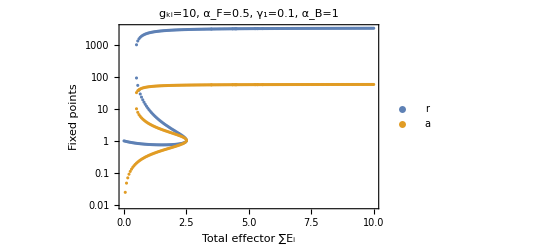

```mathematica
ListLogPlot[{rCoords,aCoords},PlotRange->{Automatic,Automatic},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB](*<>"\nE_1="<>ToString[maxE]<>"E_T"*),PlotLegends->{"r","a"},FrameLabel->{"Total effector ∑E_i","Fixed points"},LabelStyle->Directive[Black, 15],Frame->{True,True,False,False}]
```

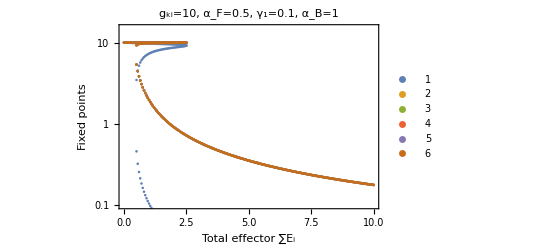

```mathematica
ListLogPlot[{k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords},PlotRange->{Automatic,{.1,15}},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB](*<>"\nE_1="<>ToString[maxE]<>"E_T"*),PlotLegends->{"1","2","3","4","5","6"},FrameLabel->{"Total effector ∑E_i","Fixed points"},LabelStyle->Directive[Black, 15],Frame->{True,True,False,False}]
```

```mathematica
(*Export["zar1_balanceTest_gki_"<>ToString[gK1]<>"_maxE_"<>ToString[maxE]<>"_ra.mx",{rCoords,aCoords}];*)
```